# Load Files

```mathematica
SetDirectory["/home/dschiebe/Documents/lanayru/PhD_Files/HexaBox_102PureIntsDone"];

Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
Get[FileNameJoin[{Directory[],"DifferentialOperator.m"}]];
$P=2^31-1;
PureIntegrals=ReadList[FileNameJoin[{NotebookDirectory[],"BubblePureInts.txt"}]];
SetDirectory[NotebookDirectory[]];

(*LaportaBasis=ReadList[FileNameJoin[{Directory[],"masters"}]];
LaportaBasis=Cases[LaportaBasis,_ptb,Infinity];*)
```

# Generate Phase-Space Point

```mathematica
tPoint=GetRandomPT[0,$P]
DeleteOldKiraRun[]
WriteNumericsFile[tPoint]
(*samplepoint=1;
SubReduList=Get[ToString[StringForm["/home/dschiebe/Documents/lanayru/PhD_Files/HexaBox_102PureIntsDone/KIRA/splitres/phasespace_00002.m",IntegerString[samplepoint,10,5]]]];
tPoint=Thread[Rule[invariants,SubReduList[[2,1]]]]

reductionRules=ReductionRules=GetReductionTableFromList[SubReduList[[2,2]]];*)


epsrepl={(ep->(4-d)/2)/.tPoint};
PureIntegralN=Expand[PureIntegrals/.tPoint/.epsrepl/.root[n_]:>PowerMod[n,1/2,$P],Modulus->$P]//EchoTiming;
diffOp=getDifferentialOperator[tPoint];
checkDifferentialOperator[tPoint,diffOp]
```

{d→680835586,mt2→61729070,s12→1198153644,s123→2031795636,s16→229271390,s23→292114709,s234→1578809511,s34→1234021570,s345→1490996089,s45→2038847441,s56→231105359}

0.049584

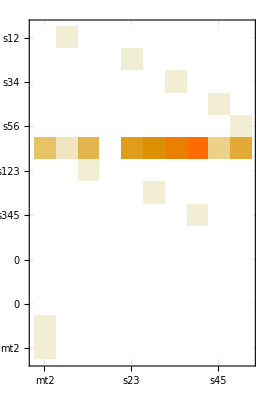

Δ6=0

∂_(RowBox[{) Δ6=0

∂_(RowBox[{) Δ6=0

∂_(RowBox[{) Δ6=0

«7 more identical outputs»

# Compute Basis Change Matrix

```mathematica
reductionRules=GetReductionTableFromFile[FileNameJoin[{NotebookDirectory[],"KIRA/results/hxb/numerics_2147483647_0.m"}]];
Ureduce=ReadList[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}]];
ExtraRelations={};
ExtraRelations=GetExtraRelationReplacements[reductionRules,tPoint];
PureIntegralN2=Expand[PureIntegralN/.reductionRules,Modulus->$P];
PureIntegralN3=Expand[PureIntegralN2/.ExtraRelations,Modulus->$P];

NonZeros=Cases[reductionRules,_hxb,Infinity]//DeleteDuplicates;
ZeroInts=Complement[Ureduce,NonZeros];
ZeroIntsRepl=Thread[Rule[ZeroInts,0]];
PureIntegralN4=Expand[PureIntegralN3/.ExtraRelations/.ZeroIntsRepl,Modulus->$P];
Cases[PureIntegralN4,_hxb,Infinity]//DeleteDuplicates//Length
SubLaporta=Cases[PureIntegralN4,_hxb,Infinity]//DeleteDuplicates;

PureIntegralN4=Expand[PureIntegralN4/.epsrepl,Modulus->$P];

BasisChangMat=Table[CoefficientArrays[PureIntegralN4[[pos]],SubLaporta],{pos,1,Length[PureIntegralN]}];
BasisChangMat=Normal[BasisChangMat[[All,2]]];
BasisChangMatInv=Inverse[BasisChangMat,Modulus->$P];
BasisChangMat//MatrixPlot
BasisChangMatInv//MatrixPlot
```

Get::noopen: Cannot open /home/dschiebe/Documents/lanayru/PhD_Files/HexaBox_102PureIntsDone/BubblesPentagons/KIRA/results/hxb/numerics_2147483647_0.m.

Part::partd: Part specification $Failed⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦2,2,1,1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦2,2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

28

Part::partw: Part 2 of {0} does not exist.

MatrixPlot::mat0: Argument {{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},«63»}⟦All,2⟧ at position 1 is not a matrix.

MatrixPlot[{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0,{1010525630,1443774128,1845527210,1422663081,1856918909,1771175218,2045340907,1614413139,1581222572,1699349061,1345246182,1080316088,2080170577,1864877758,55992469,944002688,0,0,0,0,0,0,0,0,0,0,0,0}},{0,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1063683144,559288974,1792481045,0,0,0,0,0,0,0,0,0}},{0},{0},{0},{0,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,800296774,1177327107,1877559747,1308443293,2005773842,1103173047,0,0,0}},{0},{0},{0},{0,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0}},{0,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,679460029,2088838613,868651969,1251916635,160163210,1810462012,1729061586,81417061}},{0}}⟦All,2⟧]

MatrixPlot::mat0: Argument Inverse[{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},«63»}⟦All,2⟧,Modulus→2147483647] at position 1 is not a matrix.

MatrixPlot[Inverse[{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0,{1010525630,1443774128,1845527210,1422663081,1856918909,1771175218,2045340907,1614413139,1581222572,1699349061,1345246182,1080316088,2080170577,1864877758,55992469,944002688,0,0,0,0,0,0,0,0,0,0,0,0}},{0,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1063683144,559288974,1792481045,0,0,0,0,0,0,0,0,0}},{0},{0},{0},{0,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,800296774,1177327107,1877559747,1308443293,2005773842,1103173047,0,0,0}},{0},{0},{0},{0,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0}},{0,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,679460029,2088838613,868651969,1251916635,160163210,1810462012,1729061586,81417061}},{0}}⟦All,2⟧,Modulus→2147483647]]

# Compute DE Matrix Pre IBP

```mathematica
loopMomentumScalarProductsT=Expand[loopMomentumScalarProducts/.tPoint,Modulus->$P];
mandelstamScalarProductsT=Expand[mandelstamScalarProducts/.tPoint,Modulus->$P];
DeleteList=Delete[{1,2,3,4,5,6,7,8,9,10,11},Position[tPoint[[All,1]],s16]];
Monitor[diffInts=Table[
Expand[Expand[(applyDifferentialOperator[Collect[Coefficient[diffOp,ds[invariantsnodUpperCase[[var]]]],del[___]],Expand[PureIntegrals[[intpos]]/.tPoint[[DeleteCases[DeleteList,var+1]]]/.epsrepl,Modulus->$P]]/.tPoint/.root'[x_]:>1/(2 root[x]))/.root[x_]:>PowerMod[x,1/2,$P],Modulus->$P]/.loopMomentumScalarProductsT/.mandelstamScalarProductsT,Modulus->$P],{var,1,Length[invariantsnodUpperCase]},{intpos,1,Length[PureIntegrals]}],Row[{ProgressIndicator[(var-1)*241+intpos,{1,241*10}],"  ",var,"/10 ",intpos,"/241"}]];
```

## Extra Step If Redu List does not exit yet

```mathematica
ToReduce=Cases[diffInts,_hxb,Infinity]//DeleteDuplicates//EchoFunction[Length];
Export[FileNameJoin[{NotebookDirectory[],"KIRA/ReduList.txt"}],ToReduce];
GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/ReduList.txt"}]];

ToReduce2=Cases[PureIntegralN,_hxb,Infinity]//DeleteDuplicates//EchoFunction[Length];
Export[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}],ToReduce2];
GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}]];

GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/ExtraRelationsReduList.txt"}]];

DeleteOldKiraRun[]
WriteNumericsFile[tPoint]
WriteJobFile[{"UReduList","ReduList","ExtraRelationsReduList"}]
(*WriteJobFile[{"UReduList","ReduList"}]*)
```

2238

180

# Apply IBP Reduction

```mathematica
diffIntsIBREDUCED=Expand[diffInts/.reductionRules/.ExtraRelations,Modulus->$P];
NonReduced=Cases[diffIntsIBREDUCED,_hxb,Infinity]//DeleteDuplicates//EchoFunction[Length];
NullInts2=Complement[NonReduced,SubLaporta];
diffIntsIBREDUCED=diffIntsIBREDUCED/.Thread[Rule[NullInts2,0]];
```

76

# Compute DE Matrices

```mathematica
dhxbMatrices=Table[Normal[CoefficientArrays[diffIntsIBREDUCED[[i,j]],SubLaporta]/.{0}->{0,ConstantArray[0,Length[PureIntegralN]]}][[2]],{i,1,Length[invariants]-1},{j,1,Length[SubLaporta]}];
Mplot1=MatrixPlot[Expand[dhxbMatrices[[1]].BasisChangMatInv,Modulus->$P]];
Mplot2=MatrixPlot[Expand[dhxbMatrices[[2]].BasisChangMatInv,Modulus->$P]];
Mplot3=MatrixPlot[Expand[dhxbMatrices[[3]].BasisChangMatInv,Modulus->$P]];
Mplot4=MatrixPlot[Expand[dhxbMatrices[[4]].BasisChangMatInv,Modulus->$P]];
Mplot5=MatrixPlot[Expand[dhxbMatrices[[5]].BasisChangMatInv,Modulus->$P]];
Mplot6=MatrixPlot[Expand[dhxbMatrices[[6]].BasisChangMatInv,Modulus->$P]];
Mplot7=MatrixPlot[Expand[dhxbMatrices[[7]].BasisChangMatInv,Modulus->$P]];
Mplot8=MatrixPlot[Expand[dhxbMatrices[[8]].BasisChangMatInv,Modulus->$P]];
Mplot9=MatrixPlot[Expand[dhxbMatrices[[9]].BasisChangMatInv,Modulus->$P]];
Mplot10=MatrixPlot[Expand[dhxbMatrices[[10]].BasisChangMatInv,Modulus->$P]];
GraphicsGrid[{{Mplot1,Mplot2,Mplot3,Mplot4,Mplot5},{Mplot6,Mplot7,Mplot8,Mplot9,Mplot10}}]
```

-Graphics-

$Aborted

```mathematica
sqrtSetOLD=sqrtSet
```

{(-s12+s34)^2-2 (s12+s34) s56+s56^2,-4 s12 s23 s34 (-s123+s23-s234+s56)+(-s12 s23+s12 s234-s123 s234+s123 s34-s23 s34+s23 s56)^2,-4 mt2 s12+(-mt2-s12+s345)^2,-4 mt2 s56+s56^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2,mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,-4 mt2 s12 s34 s56+mt2^2 s56^2-2 mt2 s345 s56^2+s345^2 s56^2,mt2^2 s12^2-2 mt2^2 s12 s123+mt2^2 s123^2-2 mt2^2 s12 s34+2 mt2^2 s123 s34+2 mt2 s12 s123 s34-2 mt2 s123^2 s34+mt2^2 s34^2-2 mt2 s123 s34^2+s123^2 s34^2+2 mt2 s12 s123 s345-2 mt2 s123^2 s345-2 mt2 s123 s34 s345-2 s123^2 s34 s345+s123^2 s345^2-2 mt2 s12^2 s45+2 mt2 s12 s123 s45+4 mt2 s12 s34 s45-2 mt2 s123 s34 s45+2 s12 s123 s34 s45-2 mt2 s34^2 s45-2 s123 s34^2 s45-2 s12 s123 s345 s45+2 s123 s34 s345 s45+s12^2 s45^2-2 s12 s34 s45^2+s34^2 s45^2-2 mt2 s12 s345 s56+2 mt2 s123 s345 s56-2 mt2 s34 s345 s56+2 s123 s34 s345 s56-2 s123 s345^2 s56+2 mt2 s12 s45 s56-2 mt2 s123 s45 s56+2 mt2 s34 s45 s56-4 s12 s34 s45 s56+2 s123 s34 s45 s56+2 s12 s345 s45 s56+2 s123 s345 s45 s56+2 s34 s345 s45 s56-2 s12 s45^2 s56-2 s34 s45^2 s56+s345^2 s56^2-2 s345 s45 s56^2+s45^2 s56^2,s345^2-2 s345 s45+s45^2,mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2,s16^2-2 s16 s23+s23^2-2 s16 s45-2 s23 s45+s45^2,s56 (-4 mt2 s12 s34+(mt2-s345)^2 s56),s56 (-4 mt2 s12 s34+mt2^2 s56-2 mt2 s345 s56+s345^2 s56),-mt2^2 s12^2+2 mt2^2 s12 s123-mt2^2 s123^2+2 mt2^2 s12 s34-2 mt2^2 s123 s34-2 mt2 s12 s123 s34+2 mt2 s123^2 s34-mt2^2 s34^2+2 mt2 s123 s34^2-s123^2 s34^2-2 mt2 s12 s123 s345+2 mt2 s123^2 s345+2 mt2 s123 s34 s345+2 s123^2 s34 s345-s123^2 s345^2+2 mt2 s12^2 s45-2 mt2 s12 s123 s45-4 mt2 s12 s34 s45+2 mt2 s123 s34 s45-2 s12 s123 s34 s45+2 mt2 s34^2 s45+2 s123 s34^2 s45+2 s12 s123 s345 s45-2 s123 s34 s345 s45-s12^2 s45^2+2 s12 s34 s45^2-s34^2 s45^2+2 mt2 s12 s345 s56-2 mt2 s123 s345 s56+2 mt2 s34 s345 s56-2 s123 s34 s345 s56+2 s123 s345^2 s56-2 mt2 s12 s45 s56+2 mt2 s123 s45 s56-2 mt2 s34 s45 s56+4 s12 s34 s45 s56-2 s123 s34 s45 s56-2 s12 s345 s45 s56-2 s123 s345 s45 s56-2 s34 s345 s45 s56+2 s12 s45^2 s56+2 s34 s45^2 s56-s345^2 s56^2+2 s345 s45 s56^2-s45^2 s56^2}

```mathematica
sqrtSet=sqrtSetOLD[[;;-2]]
```

{(-s12+s34)^2-2 (s12+s34) s56+s56^2,-4 s12 s23 s34 (-s123+s23-s234+s56)+(-s12 s23+s12 s234-s123 s234+s123 s34-s23 s34+s23 s56)^2,-4 mt2 s12+(-mt2-s12+s345)^2,-4 mt2 s56+s56^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2,mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,-4 mt2 s12 s34 s56+mt2^2 s56^2-2 mt2 s345 s56^2+s345^2 s56^2,mt2^2 s12^2-2 mt2^2 s12 s123+mt2^2 s123^2-2 mt2^2 s12 s34+2 mt2^2 s123 s34+2 mt2 s12 s123 s34-2 mt2 s123^2 s34+mt2^2 s34^2-2 mt2 s123 s34^2+s123^2 s34^2+2 mt2 s12 s123 s345-2 mt2 s123^2 s345-2 mt2 s123 s34 s345-2 s123^2 s34 s345+s123^2 s345^2-2 mt2 s12^2 s45+2 mt2 s12 s123 s45+4 mt2 s12 s34 s45-2 mt2 s123 s34 s45+2 s12 s123 s34 s45-2 mt2 s34^2 s45-2 s123 s34^2 s45-2 s12 s123 s345 s45+2 s123 s34 s345 s45+s12^2 s45^2-2 s12 s34 s45^2+s34^2 s45^2-2 mt2 s12 s345 s56+2 mt2 s123 s345 s56-2 mt2 s34 s345 s56+2 s123 s34 s345 s56-2 s123 s345^2 s56+2 mt2 s12 s45 s56-2 mt2 s123 s45 s56+2 mt2 s34 s45 s56-4 s12 s34 s45 s56+2 s123 s34 s45 s56+2 s12 s345 s45 s56+2 s123 s345 s45 s56+2 s34 s345 s45 s56-2 s12 s45^2 s56-2 s34 s45^2 s56+s345^2 s56^2-2 s345 s45 s56^2+s45^2 s56^2,s345^2-2 s345 s45+s45^2,mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2,s16^2-2 s16 s23+s23^2-2 s16 s45-2 s23 s45+s45^2,s56 (-4 mt2 s12 s34+(mt2-s345)^2 s56),s56 (-4 mt2 s12 s34+mt2^2 s56-2 mt2 s345 s56+s345^2 s56)}

```mathematica
tPoint=GetRandomPT[0,$P]
```

{d→1718387072,mt2→1594523214,s12→1337310463,s123→205997118,s16→189341326,s23→1315042329,s234→38966380,s34→1194656482,s345→830513889,s45→1388831432,s56→352951260}

```mathematica
a=-mt2^2 s12^2+2 mt2^2 s12 s123-mt2^2 s123^2+2 mt2^2 s12 s34-2 mt2^2 s123 s34-2 mt2 s12 s123 s34+2 mt2 s123^2 s34-mt2^2 s34^2+2 mt2 s123 s34^2-s123^2 s34^2-2 mt2 s12 s123 s345+2 mt2 s123^2 s345+2 mt2 s123 s34 s345+2 s123^2 s34 s345-s123^2 s345^2+2 mt2 s12^2 s45-2 mt2 s12 s123 s45-4 mt2 s12 s34 s45+2 mt2 s123 s34 s45-2 s12 s123 s34 s45+2 mt2 s34^2 s45+2 s123 s34^2 s45+2 s12 s123 s345 s45-2 s123 s34 s345 s45-s12^2 s45^2+2 s12 s34 s45^2-s34^2 s45^2+2 mt2 s12 s345 s56-2 mt2 s123 s345 s56+2 mt2 s34 s345 s56-2 s123 s34 s345 s56+2 s123 s345^2 s56-2 mt2 s12 s45 s56+2 mt2 s123 s45 s56-2 mt2 s34 s45 s56+4 s12 s34 s45 s56-2 s123 s34 s45 s56-2 s12 s345 s45 s56-2 s123 s345 s45 s56-2 s34 s345 s45 s56+2 s12 s45^2 s56+2 s34 s45^2 s56-s345^2 s56^2+2 s345 s45 s56^2-s45^2 s56^2
```

-mt2^2 s12^2+2 mt2^2 s12 s123-mt2^2 s123^2+2 mt2^2 s12 s34-2 mt2^2 s123 s34-2 mt2 s12 s123 s34+2 mt2 s123^2 s34-mt2^2 s34^2+2 mt2 s123 s34^2-s123^2 s34^2-2 mt2 s12 s123 s345+2 mt2 s123^2 s345+2 mt2 s123 s34 s345+2 s123^2 s34 s345-s123^2 s345^2+2 mt2 s12^2 s45-2 mt2 s12 s123 s45-4 mt2 s12 s34 s45+2 mt2 s123 s34 s45-2 s12 s123 s34 s45+2 mt2 s34^2 s45+2 s123 s34^2 s45+2 s12 s123 s345 s45-2 s123 s34 s345 s45-s12^2 s45^2+2 s12 s34 s45^2-s34^2 s45^2+2 mt2 s12 s345 s56-2 mt2 s123 s345 s56+2 mt2 s34 s345 s56-2 s123 s34 s345 s56+2 s123 s345^2 s56-2 mt2 s12 s45 s56+2 mt2 s123 s45 s56-2 mt2 s34 s45 s56+4 s12 s34 s45 s56-2 s123 s34 s45 s56-2 s12 s345 s45 s56-2 s123 s345 s45 s56-2 s34 s345 s45 s56+2 s12 s45^2 s56+2 s34 s45^2 s56-s345^2 s56^2+2 s345 s45 s56^2-s45^2 s56^2

```mathematica
b=mt2^2 s12^2-2 mt2^2 s12 s123+mt2^2 s123^2-2 mt2^2 s12 s34+2 mt2^2 s123 s34+2 mt2 s12 s123 s34-2 mt2 s123^2 s34+mt2^2 s34^2-2 mt2 s123 s34^2+s123^2 s34^2+2 mt2 s12 s123 s345-2 mt2 s123^2 s345-2 mt2 s123 s34 s345-2 s123^2 s34 s345+s123^2 s345^2-2 mt2 s12^2 s45+2 mt2 s12 s123 s45+4 mt2 s12 s34 s45-2 mt2 s123 s34 s45+2 s12 s123 s34 s45-2 mt2 s34^2 s45-2 s123 s34^2 s45-2 s12 s123 s345 s45+2 s123 s34 s345 s45+s12^2 s45^2-2 s12 s34 s45^2+s34^2 s45^2-2 mt2 s12 s345 s56+2 mt2 s123 s345 s56-2 mt2 s34 s345 s56+2 s123 s34 s345 s56-2 s123 s345^2 s56+2 mt2 s12 s45 s56-2 mt2 s123 s45 s56+2 mt2 s34 s45 s56-4 s12 s34 s45 s56+2 s123 s34 s45 s56+2 s12 s345 s45 s56+2 s123 s345 s45 s56+2 s34 s345 s45 s56-2 s12 s45^2 s56-2 s34 s45^2 s56+s345^2 s56^2-2 s345 s45 s56^2+s45^2 s56^2
```

mt2^2 s12^2-2 mt2^2 s12 s123+mt2^2 s123^2-2 mt2^2 s12 s34+2 mt2^2 s123 s34+2 mt2 s12 s123 s34-2 mt2 s123^2 s34+mt2^2 s34^2-2 mt2 s123 s34^2+s123^2 s34^2+2 mt2 s12 s123 s345-2 mt2 s123^2 s345-2 mt2 s123 s34 s345-2 s123^2 s34 s345+s123^2 s345^2-2 mt2 s12^2 s45+2 mt2 s12 s123 s45+4 mt2 s12 s34 s45-2 mt2 s123 s34 s45+2 s12 s123 s34 s45-2 mt2 s34^2 s45-2 s123 s34^2 s45-2 s12 s123 s345 s45+2 s123 s34 s345 s45+s12^2 s45^2-2 s12 s34 s45^2+s34^2 s45^2-2 mt2 s12 s345 s56+2 mt2 s123 s345 s56-2 mt2 s34 s345 s56+2 s123 s34 s345 s56-2 s123 s345^2 s56+2 mt2 s12 s45 s56-2 mt2 s123 s45 s56+2 mt2 s34 s45 s56-4 s12 s34 s45 s56+2 s123 s34 s45 s56+2 s12 s345 s45 s56+2 s123 s345 s45 s56+2 s34 s345 s45 s56-2 s12 s45^2 s56-2 s34 s45^2 s56+s345^2 s56^2-2 s345 s45 s56^2+s45^2 s56^2

```mathematica
FullSimplify[a/b]
```

-1

```mathematica
diffInts[[1]]
```